### Markov’s Inequality

```mathematica
a = 1;
b = 2;
EX = Expectation[x, x\[Distributed]ExponentialDistribution[20]]
```

1/20

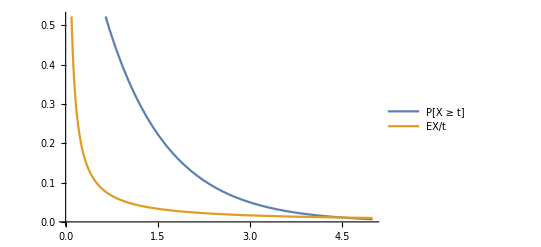

```mathematica
Plot[{NProbability[x≥t,x\[Distributed]ExponentialDistribution[r]],EX/t}, {t, 0, 5},PlotLegends-> {"P[X ≥ t]","EX/t"}]
```